```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

## Importing data

```mathematica
(*observed error, flag == 0,
 error grid, flag == 1 and 
error velocity flag == 2
num sol flag == 3
adjoint sol == 4*)
importdata[cycle_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/error_observed_cycle",ToString[cycle],".txt"],
flag == 1,
filename=StringJoin["../",outputdir,"/error_grid_cycle",ToString[cycle],".txt"],

flag == 2,
filename=StringJoin["../",outputdir,"/error_velocity_cycle",ToString[cycle],".txt"],
flag == 3,
filename=StringJoin["../",outputdir,"/result_cycle",ToString[cycle],".txt"],
flag == 4,
filename=StringJoin["../",outputdir,"/resultAdj_cycle",ToString[cycle],".txt"],
flag == 5,
filename=StringJoin["../",outputdir,"/fe_index_cycle",ToString[cycle],".txt"]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]
]

SortData[data_]:=Module[{indices},
indices = Ordering[data⟦All,1⟧,All,GreaterEqual];
data⟦indices,All⟧
]
```

## Results

```mathematica
M6sol = GetSolutionPoisson[6,0.1,1,bcMBC[6]]⟦3⟧;
M50sol = GetSolutionPoisson[50,0.1,1,bcMBC[50]]⟦3⟧;
```

```mathematica
Clear[errorObs,errorGrid,errorVelocity,resultPrimal,resultAdj,feIndex];
```

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"2x1v_moments_wall_Adp"];
errorGrid[cycle]=importdata[cycle,1,"2x1v_moments_wall_Adp"];
errorVelocity[cycle]=importdata[cycle,2,"2x1v_moments_wall_Adp"];
resultPrimal[cycle]=importdata[cycle,3,"2x1v_moments_wall_Adp"];
resultAdj[cycle]=importdata[cycle,4,"2x1v_moments_wall_Adp"];
feIndex[cycle]=importdata[cycle,5,"2x1v_moments_wall_Adp"],{cycle,0,4}];
```

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_observed_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_grid_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/error_velocity_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/result_cycle4.txt

Reading Data from...

../2x1v_moments_wall_Adp/fe_index_cycle4.txt

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

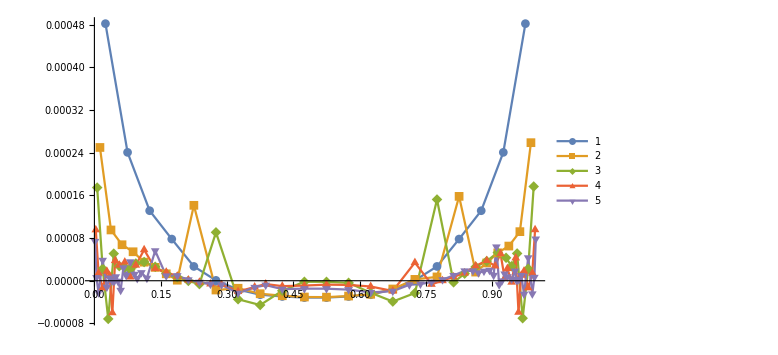

```mathematica
ListPlot[{SortData[errorGrid[0]]⟦All,{1,3}⟧,SortData[errorGrid[1]]⟦All,{1,3}⟧,SortData[errorGrid[2]]⟦All,{1,3}⟧,SortData[errorGrid[3]]⟦All,{1,3}⟧,SortData[errorGrid[4]]⟦All,{1,3}⟧},ImageSize->Large,Joined->True,PlotRange->Full,PlotLegends->Automatic,PlotMarkers->Automatic]
```

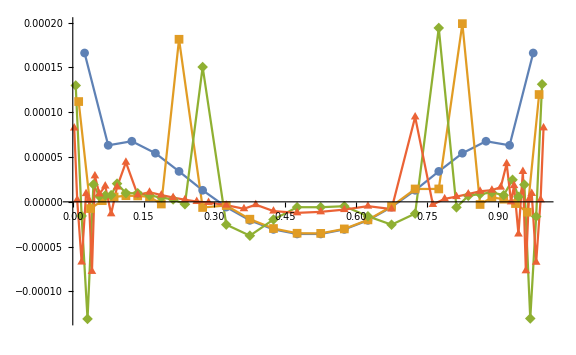

```mathematica
ListPlot[{SortData[errorVelocity[0]]⟦All,{1,3}⟧,SortData[errorVelocity[1]]⟦All,{1,3}⟧,SortData[errorVelocity[2]]⟦All,{1,3}⟧,SortData[errorVelocity[3]]⟦All,{1,3}⟧(*,SortData[errorVelocity[4]]⟦All,{1,3}⟧*)},ImageSize->Large,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

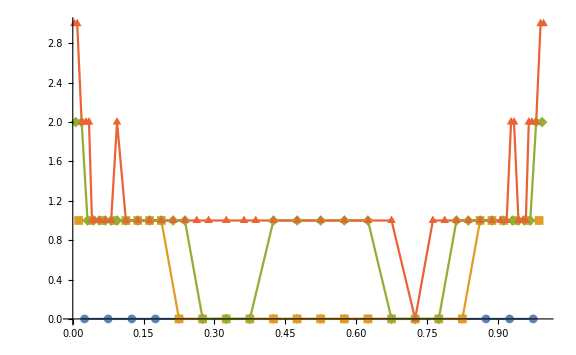

```mathematica
ListPlot[{SortData[feIndex[0]]⟦All,{1,3}⟧,SortData[feIndex[1]]⟦All,{1,3}⟧,SortData[feIndex[2]]⟦All,{1,3}⟧,SortData[feIndex[3]]⟦All,{1,3}⟧(*,SortData[errorVelocity[4]]⟦All,{1,3}⟧*)},ImageSize->Large,Joined->True,PlotRange->Full,PlotMarkers->Automatic]
```

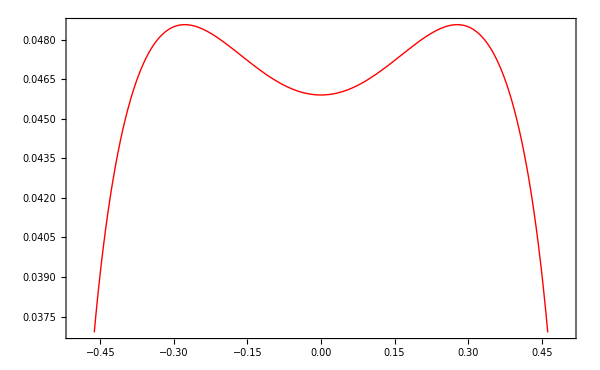

```mathematica
Plot[M50sol,{x,-0.5,0.5}]
```

```mathematica
NIntegrate[M50sol-M6sol,{x,-0.5,0.5}]/0.001153
```

1.26059

```mathematica
convgAdp = Import["../2x1v_moments_wall_Adp/convergence_table_adaptive.txt","Table"];
convgUni = Import["../2x1v_moments_wall_Adp/convergence_table_uniform.txt","Table"];
```

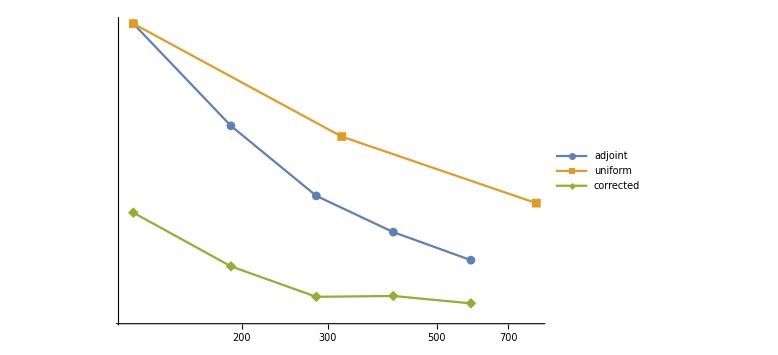

```mathematica
ListLogLogPlot[{convgAdp⟦2;;-1,{6,7}⟧,convgUni⟦2;;-1,{6,7}⟧,convgAdp⟦2;;-1,{6,13}⟧(*,convgAdp⟦2;;-1,{6,9}⟧,convgAdp⟦2;;-1,{6,11}⟧*)},Joined->True,PlotLegends->{"adjoint","uniform","corrected"},PlotMarkers->Automatic,ImageSize->Large,PlotRange->Full]
```

```mathematica
CForm[Chop[Simplify[GetSolutionPoisson[14,0.1,1,bcMBC[14]]⟦3⟧]]]/.{Power->pow,Cosh->cosh}
```

0.05653013082799942 - 0.00003792694823015286*cosh(1.64277980395364*x) - 0.0014402108667994624*cosh(2.0483113377580193*x) - 
   0.00530163981896668*cosh(2.6857066212139475*x) - 0.003996181490901356*cosh(4.230009784703013*x) - 
   0.00006758700357029971*cosh(12.325411809002668*x) + 0.13333333333333333*pow(x,2) - 0.2777777777777778*pow(x,4)

## Validate Grid Refinement

```mathematica
M6sol = GetSolutionPoisson[6,0.1,1,bcMBC[6]]⟦3⟧;
M6adj = GetAdjointPoisson[6,0.1,bcMBC[6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

### M6

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"2x1v_moments_wall_Adp/validate_grid_error/M6"];
errorGrid[cycle]=importdata[cycle,1,"2x1v_moments_wall_Adp/validate_grid_error/M6"];
resultPrimal[cycle]=importdata[cycle,3,"2x1v_moments_wall_Adp/validate_grid_error/M6"];
resultAdj[cycle]=importdata[cycle,4,"2x1v_moments_wall_Adp/validate_grid_error/M6"];,{cycle,0,3}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_observed_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/error_grid_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/result_cycle3.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/resultAdj_cycle3.txt

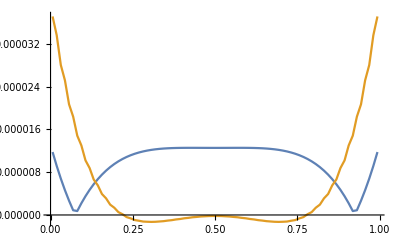

```mathematica
ListPlot[{Abs[SortData[errorObs[2]]⟦All,{1,3}⟧],SortData[errorVelocity[2]]⟦All,{1,3}⟧},Joined->True]
```

```mathematica
Length[errorObs[3]⟦All,1⟧]
```

160

#### compute error

```mathematica
IntegratexAy[x_,A_,y_,lim1_,lim2_]:=Module[{temp},
temp = A.y;
Total[Table[NIntegrate[x⟦ii⟧[t]temp⟦ii⟧,{t,lim1,lim2}],{ii,1,Length[x]}]]
]
```

```mathematica
ComputeError[adjoint_,primal_]:=Module[{adjInt,faces,dx,Ax,neqn,Amod,v,d,error,gridPoints,cellContri,temp,AminusR,AminusL,uR,uM,uL,zR,zL,facesAdj},

neqn = Length[adjoint⟦1⟧]-2;
adjInt = Table[Interpolation[adjoint⟦All,{1,ii}⟧],{ii,3,Length[adjoint⟦1⟧]}];
dx = 1/Length[adjoint];
faces = Range[0,1,dx];
gridPoints = Length[faces]-1;
cellContri = Table[0,{ii,1,gridPoints}];
error=Table[0,{ii,1,gridPoints}];

Ax = AA[neqn];
{d,v}=N[Eigensystem[Ax]];
d = Abs[d];
v = Transpose[v];
Amod = v.DiagonalMatrix[d].Inverse[v];
(*
Do[cellContri⟦ii⟧=NIntegrate[(x-0.5)^2 adjInt⟦3⟧[x],{x,faces⟦ii⟧,faces⟦ii+1⟧}];(* + IntegratexAy[adjInt,returnP[neqn]/0.1,primal⟦ii,3;;-1⟧,faces⟦ii⟧,faces⟦ii+1⟧]*);,{ii,1,Length[faces]-1}];*)
AminusR = Amod-Ax;
AminusL = Amod+Ax;

facesAdj = Table[Table[jj[ii],{jj,adjInt}],{ii,faces}];

Do[
uR = primal⟦ii+1,3;;-1⟧;
uM = primal⟦ii,3;;-1⟧;
uL = primal⟦ii-1,3;;-1⟧;
zR = facesAdj⟦ii+1⟧;
zL = facesAdj⟦ii⟧;
cellContri⟦ii⟧+=(-zR.AminusR.(uM-uR))/2-(zL.AminusL.(uM-uL))/2;,{ii,2,Length[faces]-2}];

Transpose[{primal⟦All,1⟧,cellContri}]
]
```

```mathematica
Clear[trial]
```

```mathematica
test = ComputeError[SortData[resultAdj[0]],SortData[resultPrimal[0]]];
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
returnP[6]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,-1,0,0},{0,0,0,0,-1,0},{0,0,0,0,0,-1}}

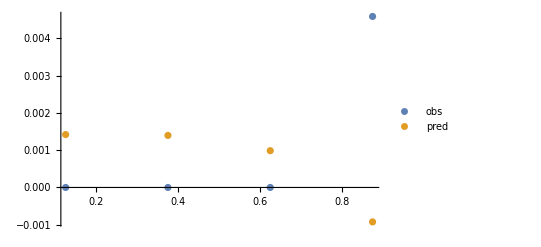

```mathematica
ListPlot[{errorObs[0]⟦All,{1,3}⟧,errorGrid[0]⟦All,{1,3}⟧},PlotLegends->{"obs","pred"},PlotRange->Full]
```

```mathematica
M6num = Interpolation[resultPrimal[0]⟦All,{1,5}⟧];
```

```mathematica
trial = GetSolution[6,0.1,1,bcMBC[6]]⟦3⟧;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

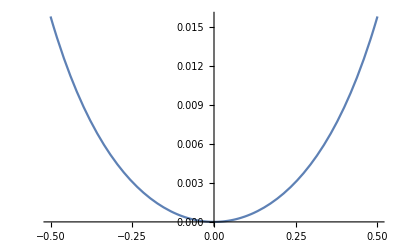

```mathematica
Plot[x(trial-M6num[x+0.5]),{x,-0.5,0.5}]
```

```mathematica
CForm[Simplify[GetSolution[6,0.1,1,bcMBC[6]]⟦3⟧]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

0.9950211932019232*x + 0.009745323921348737*Sinh(4.47213595499958*x)

```mathematica
z = {1.634 10^-2,2.350 10^-3,1.192 10^-2,4.086 10^-3,-1.935  10^-4,-6.933 10^-4};
u = {4.406 10^-1,-7.336 10^-2,-3.108 10^-1,-1.370 10^-1,8.456 10^-3,9.692 10^-3};
```

```mathematica
(z.returnP[6].u)/0.1
```

0.00568138

### 1D wave equation

```mathematica
Do[
errorObs[cycle]=importdata[cycle,0,"1D_wave"];
errorGrid[cycle]=importdata[cycle,1,"1D_wave"];
resultPrimal[cycle]=importdata[cycle,3,"1D_wave"];
resultAdj[cycle]=importdata[cycle,4,"1D_wave"];,{cycle,0,4}];
```

Reading Data from...

../1D_wave/error_observed_cycle0.txt

Reading Data from...

../1D_wave/error_grid_cycle0.txt

Reading Data from...

../1D_wave/result_cycle0.txt

Reading Data from...

../1D_wave/resultAdj_cycle0.txt

Reading Data from...

../1D_wave/error_observed_cycle1.txt

Reading Data from...

../1D_wave/error_grid_cycle1.txt

Reading Data from...

../1D_wave/result_cycle1.txt

Reading Data from...

../1D_wave/resultAdj_cycle1.txt

Reading Data from...

../1D_wave/error_observed_cycle2.txt

Reading Data from...

../1D_wave/error_grid_cycle2.txt

Reading Data from...

../1D_wave/result_cycle2.txt

Reading Data from...

../1D_wave/resultAdj_cycle2.txt

Reading Data from...

../1D_wave/error_observed_cycle3.txt

Reading Data from...

../1D_wave/error_grid_cycle3.txt

Reading Data from...

../1D_wave/result_cycle3.txt

Reading Data from...

../1D_wave/resultAdj_cycle3.txt

Reading Data from...

../1D_wave/error_observed_cycle4.txt

Reading Data from...

../1D_wave/error_grid_cycle4.txt

Reading Data from...

../1D_wave/result_cycle4.txt

Reading Data from...

../1D_wave/resultAdj_cycle4.txt

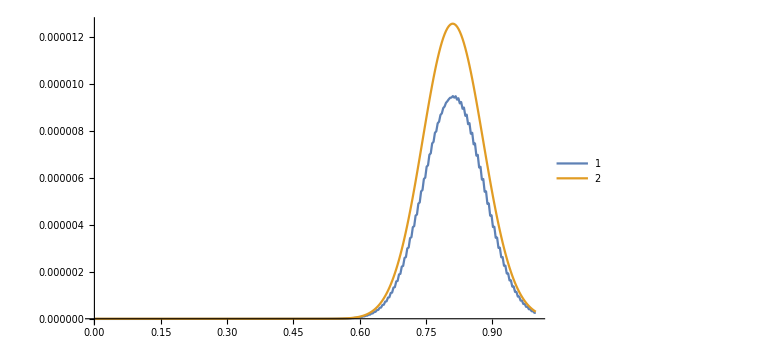

```mathematica
ListPlot[{errorGrid[4]⟦All,{1,3}⟧,errorObs[4]⟦All,{1,3}⟧},PlotLegends->Automatic,PlotRange->Full,Joined->True,ImageSize->Large]
```

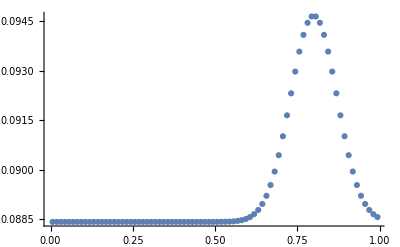

```mathematica
ListPlot[{resultAdj[2]⟦All,{1,3}⟧}]
```

```mathematica
AA[4].D[{Sin[π x],0,0,0},x]
```

{0,π Cos[π x],0,0}

```mathematica
trial = Interpolation[resultPrimal[2]⟦All,{1,3}⟧];
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

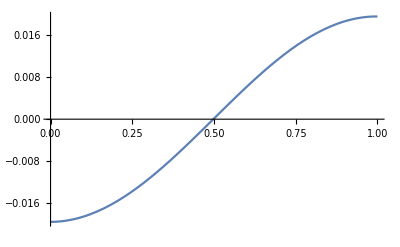

```mathematica
Plot[{Sin[π x]-trial[x]},{x,0,1},PlotRange->Full]
```

### manufactured M = 4

```mathematica
foldername = "2x1v_moments_wall_Adp/validate_grid_error/M6/";
Do[
errorObs[cycle]=importdata[cycle,0,foldername];
errorGrid[cycle]=importdata[cycle,1,foldername];
resultPrimal[cycle]=importdata[cycle,3,foldername];
resultAdj[cycle]=importdata[cycle,4,foldername];,{cycle,0,2}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_observed_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_grid_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//result_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//resultAdj_cycle0.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_observed_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_grid_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//result_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//resultAdj_cycle1.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_observed_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//error_grid_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//result_cycle2.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6//resultAdj_cycle2.txt

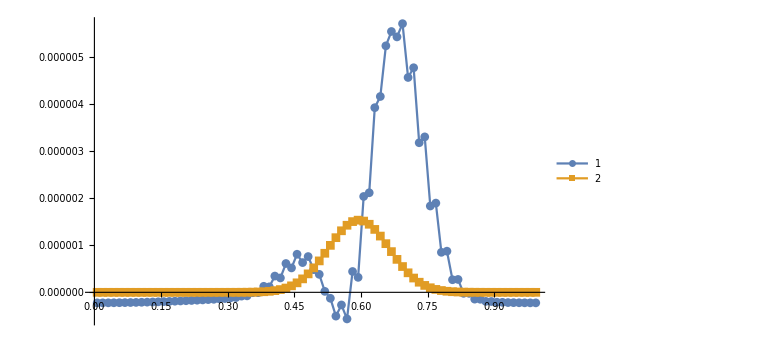

```mathematica
ListPlot[{errorGrid[2]⟦All,{1,3}⟧,errorObs[2]⟦All,{1,3}⟧},PlotLegends->Automatic,PlotRange->Full,Joined->True,ImageSize->Large,PlotMarkers->Automatic]
```

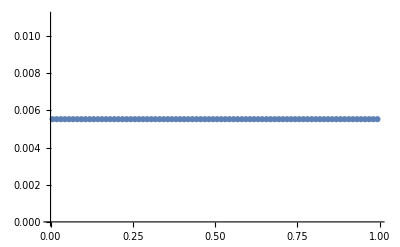

```mathematica
ListPlot[{resultAdj[2]⟦All,{1,4}⟧},PlotRange->Full]
```

```mathematica
trial = Interpolation[resultPrimal[2]⟦All,{1,4}⟧];
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

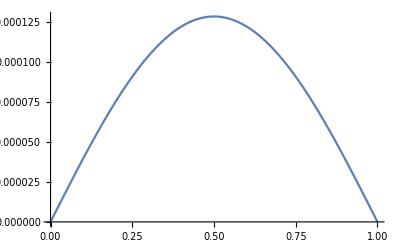

```mathematica
Plot[{Sin[π x]-trial[x]},{x,0,1}]
```